# Inverse Transform Sampling

## Example 4: Beta Distribution

## SCIMATH202 Project: Spring 2021 University College Roosevelt Robin van den Berg

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
```

```mathematica
n=50000;
(* This defines our sample size n. *)
```

```mathematica
f[x_]:= Exp[-x];
```

```mathematica
Finv[x_]:=-Log[Abs[1-x]]
(* This defines the inverse CDF of the Exponential distribution with parameter 1. *)
```

```mathematica
data=Table[,{n}];
```

```mathematica
newdata1=Table[,{5000}];
```

```mathematica
newdata2=Table[,{5000}];
(* This creates tables where the data will be stored. *)
```

```mathematica
Do[
mylist={};
U=RandomVariate[UniformDistribution[{0,1}]];
Y=Finv[U] ;
AppendTo[mylist,Y];
data[[ii]]=mylist;
,{ii,1,n}];
(* This generates a random sample of size n from the above Exponential distribution using the ITM. *)
```

```mathematica
Do[
newlist1={};
sumexp=Total[RandomSample[data,5]] ;
AppendTo[newlist1,sumexp];
newdata1[[ii]]=newlist1;
,{ii,1,5000}];
(* This generates a random sample of size 5000 from the Gamma distribution by taking 5000 mini samples of size 5 from the Exponential Distribution and computing the sample totals. *)
```

```mathematica
Do[
newlist2={};
sumexp=Total[RandomSample[data,10]] ;
AppendTo[newlist2,sumexp];
newdata2[[ii]]=newlist2;
,{ii,1,5000}];
(* This generates a random sample of size 5000 from the Gamma distribution by taking 5000 mini samples of size 10 from the Exponential Distribution and computing the sample totals. *)
```

```mathematica
plotnewdata1=Flatten[newdata1,2];
plotnewdata2=Flatten[newdata2,2];
```

```mathematica
g1[x_]:=(x^(5-1)Exp[-x])/((5-1)!);
```

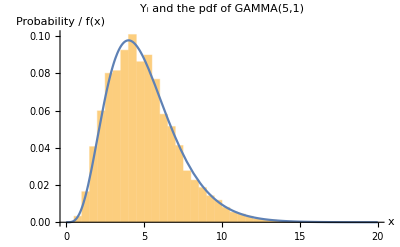

```mathematica
p1=Histogram[plotnewdata1,{0,20,0.5},"Probability"];
p2=Plot[1/2 g1[x],{x,0,20}];
Show[p1,p2,PlotLabel-> "Y_i and the pdf of GAMMA(5,1)", AxesLabel-> {"x","Probability / f(x)"}]
```

```mathematica
g2[x_]:=(x^(10-1)Exp[-x])/((10-1)!);
```

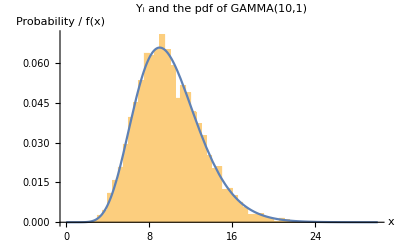

```mathematica
p3=Histogram[plotnewdata2,{0,30,0.5},"Probability"];
p4=Plot[0.5g2[x],{x,0,30}];
Show[p3,p4,PlotLabel-> "Y_i and the pdf of GAMMA(10,1)", AxesLabel-> {"x","Probability / f(x)"}]
```

```mathematica
beta=plotnewdata1/(plotnewdata1+plotnewdata2);
(* This generates a random sample of size 5000 from the Beta distribution by combining the 2 Gamma distributed random variables generated above. *)
```

```mathematica
plotbeta=Flatten[beta,1];
```

```mathematica
b[x_]:=1/Beta[5,10] x^(5-1)(1-x)^(10-1);
```

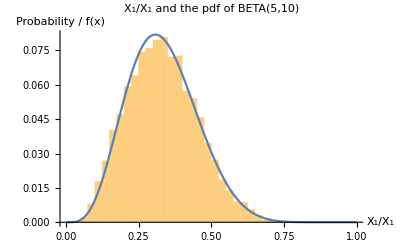

```mathematica
p5=Histogram[plotbeta,{0,1,0.025},"Probability"];
p6=Plot[0.025b[x],{x,0,1}];
Show[p5,p6,PlotLabel-> "X_1/X_1 and the pdf of BETA(5,10)", AxesLabel-> {"X_1/X_1","Probability / f(x)"}]
```